## Cycles of a Permutation

```mathematica
randomPermutation[n_]:=Module[{nList=Range[n],perm=List[]},
					Do [choose=RandomInteger[{1,n-i}];AppendTo[perm,nList[[choose]]];nList=Delete[nList, choose],{i,0,n-1}];
perm]
```

```mathematica
randomPartition[n_]:=Module[{perm=randomPermutation[n]},
lengths=Length/@PermutationCycles[perm,Identity];
Reverse[Sort[lengths]]]
```

```mathematica
partitionsGen=Table[randomPartition[10000],{i,1000}]
```

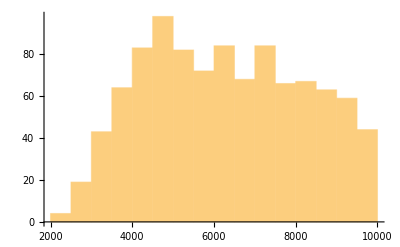

```mathematica
Histogram[Max/@partitionsGen]
```

```mathematica
10000/6295.06
```

1.58855

```mathematica
N[Mean[Max/@partitionsGen]]
```

6295.06

```mathematica
test={{1,2},{3,4}}
```

{{1,2},{3,4}}

```mathematica
Max[test]
```

4

```mathematica
Max/@test
```

{2,4}

```mathematica
Mean[Max[#&]/.partitionsGen]
```

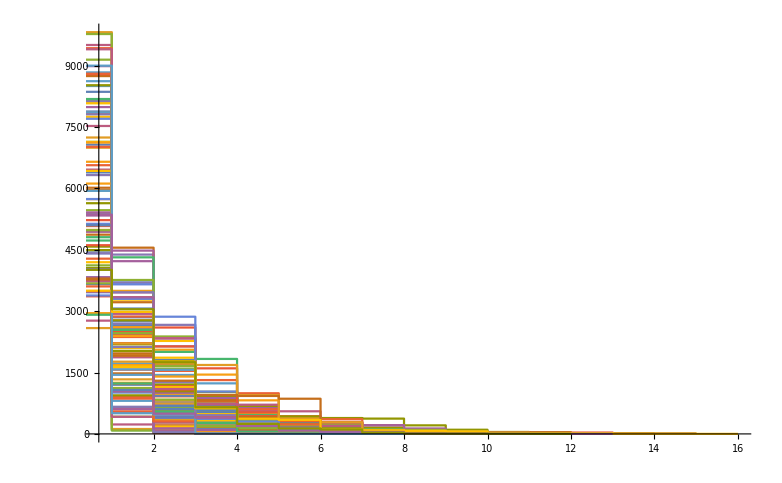

```mathematica
ListStepPlot[partitionsGen,Left,PlotRange->Full]
```

## Longest Increasing Subsequence of Partition

```mathematica
longestIncreasing[perm_]:=Module[{longestIncList={1}},
		Do[incIndices=Select[Range[i-1],perm[[#]]<perm[[i]]&];
		AppendTo[longestIncList, If[Length[incIndices]>=1,Max[longestIncList[[incIndices]]]+1,1]],
		{i,2,Length[perm]}];
		{Max[longestIncList],perm[[PositionLargest[longestIncList]]]}]
```

```mathematica
longestThousand=Table[longestIncreasing[randomPermutation[1000]],{i,100}]
```

{{58,{990}},{58,{978,973,966}},{60,{997}},{60,{1000}},{55,{998,997}},{57,{983,961,895}},{53,{994}},{57,{972,965}},{59,{1000,977,874}},{60,{997}},{59,{983,968,945}},{59,{991,987,955}},{59,{954}},{58,{995}},{58,{998,995}},{55,{985,984,980,952}},{57,{964}},{63,{989}},{59,{963}},{56,{962}},{52,{945,943}},{60,{995,947}},{63,{993}},{57,{929}},{55,{983}},{63,{975}},{59,{999,996}},{58,{994}},{58,{1000}},{55,{994}},{57,{995}},{57,{989,957,939}},{63,{993,977}},{56,{991,951,943}},{60,{988}},{58,{992,984,963,958}},{56,{999,995}},{54,{994,962,954}},{58,{982}},{61,{964}},{59,{979}},{58,{946}},{59,{941}},{56,{979}},{59,{965}},{56,{946}},{61,{999,987,983}},{57,{996,990}},{59,{925}},{62,{986}},{59,{995}},{58,{995,991,987}},{58,{932}},{61,{986}},{63,{999,979}},{55,{965,956,949,906}},{57,{970,929,924}},{59,{994}},{57,{985,982,974,972,944}},{57,{996,979,945,893}},{58,{992}},{60,{996,995}},{62,{949}},{60,{998}},{53,{978}},{55,{997}},{59,{1000}},{57,{987}},{61,{1000}},{60,{990}},{58,{995,986}},{58,{908}},{55,{1000,995,977}},{58,{993,981}},{66,{994}},{55,{999}},{55,{961,955}},{54,{946}},{57,{971}},{61,{997,981}},{59,{981}},{63,{987,981}},{58,{994}},{58,{971}},{59,{990,974}},{57,{990}},{58,{996,991,988,943,935,921}},{59,{989,980,970,958}},{56,{994}},{61,{996}},{58,{993,990}},{57,{965}},{55,{998,996}},{59,{979,976}},{57,{1000,912,901}},{61,{978}},{57,{992,954,908}},{61,{998,947}},{58,{975}},{62,{972}}}

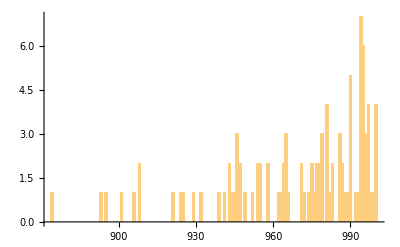

```mathematica
Histogram[Min[#[[2]]]&/@longestThousand,100]
```

```mathematica
ArgMax[x,{1,2,3}]
```

ArgMax::ivar: 1 is not a valid variable.

ArgMax[x,{1,2,3}]

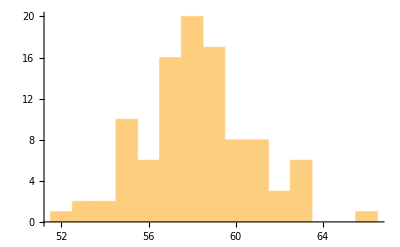

```mathematica
Histogram[#[[1]]&/@longestThousand,20]
```

## Stepwise (one cell at a time)

```mathematica
stepIndices[p_]:=Module[{stepList={1},pcopy=p},
				Do[
				stepList=If[pcopy[[i-1]]>pcopy[[i]],AppendTo[stepList,i],stepList],{i,2,Length[pcopy]}];
				stepList]
```

```mathematica
stepIndices[{8062,1661,89,84,70,25,5,2,1,1}]
```

{1,2,3,4,5,6,7,8,9,11}

```mathematica
stepPartition[n_]:=Module[{p={1},sample=0},
				Do[p=AppendTo[p,0];
				sample=RandomChoice[stepIndices[p]];
				p[[sample]]+=1,{i,1,n-1}];
				p]
```

```mathematica
stepPartitionsGen=Table[stepPartition[1000],{i,1,100}]
```

```mathematica
steps=ListStepPlot[stepPartitionsGen, Left, PlotRange -> {{0, 100}, {0, 100}}]
```

-Graphics-

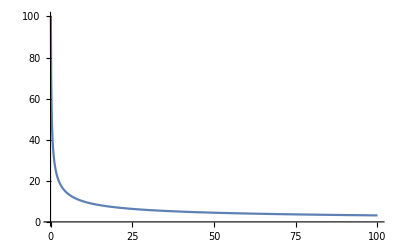

```mathematica
recip=Plot[Sqrt[1000]/Power[x,0.5],{x,0,100}, PlotRange->{0,100}]
```

```mathematica
Show[steps, recip]
```

-Graphics-

```mathematica
NIntegrate[Power[(Power[2,1.7915]-Power[x,1.7915]),1/1.7915],{x,0,2}]
```

3.00002

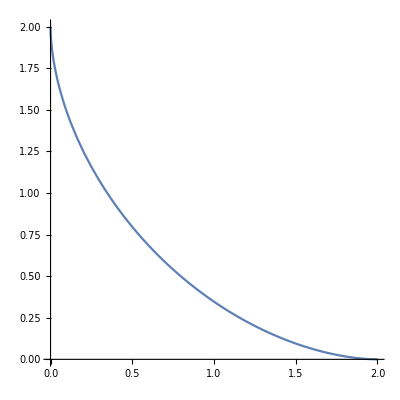

```mathematica
Plot[2-Power[(Power[2,1.7915]-Power[2-x,1.7915]),1/1.7915],{x,0,2},AspectRatio->1]
```

```mathematica
val=N[Log[2]/Log[Pi]]
```

0.605512

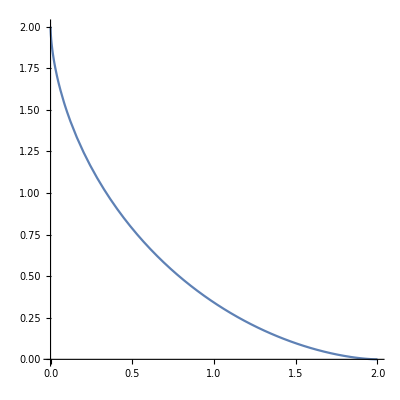

```mathematica
Plot[Power[(Power[2,val]-Power[x,val]),1/val],{x,0,2},AspectRatio->1]
```

```mathematica
NIntegrate[Power[(Power[2,Log[2]/Log[Pi]]-Power[x,Log[2]/Log[Pi]]),(Log[Pi]/Log[2])],{x,0,2},WorkingPrecision->5]
```

0.99458